```mathematica
SetDirectory["~/jennaproject/data"];
```

```mathematica
kvals=Import["kvals.txt","List"][[1;;420]];
plin=Import["plin.txt","List"][[1;;420]];
b1b2=Import["b1b2.txt","List"][[1;;420]];
b1br=Import["b1br.txt","List"][[1;;420]];
b2b2=Import["b2b2.txt","List"][[1;;420]];
b2br=Import["b2br.txt","List"][[1;;420]];
brbr=Import["brbr.txt","List"][[1;;420]];
tknw=Import["tk_nowiggle.dat","Table"];
```

```mathematica
Dimensions[tknw]
Dimensions[kvals]
```

{3000,2}

{420}

```mathematica
ns=0.966;
```

```mathematica
plinfunc=Interpolation[{kvals,plin}ᵀ];
tknwfunc=Interpolation[tknw];
```

### plin fit

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

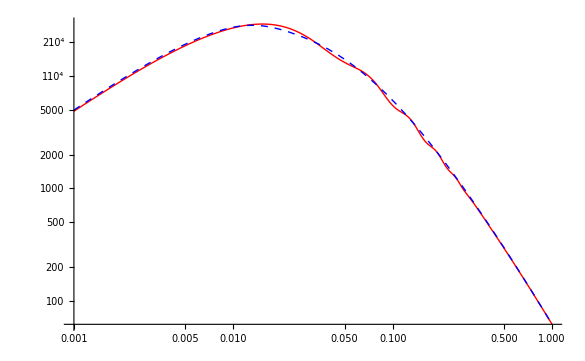

```mathematica
psnwfunc[k_]:=4.0*10^6*k^ns*tknwfunc[k]^2;
LogLogPlot[{plinfunc[k],psnwfunc[k]},{k,0.001,1},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}]
```

### b1b2 fit

```mathematica
b1b2func=Interpolation[{kvals,b1b2}ᵀ];
b1b2nw=Fit[{kvals[[1;;420;;5]],b1b2[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

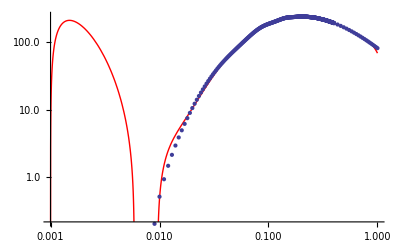

```mathematica
ϕ12=ListLogLogPlot[{kvals,b1b2}ᵀ,PlotStyle->Thick];
ω12=LogLogPlot[b1b2nw,{x,0.001,1},PlotStyle->Red];
Show[ω12,ϕ12]
```

### b1br fit

```mathematica
b1brfunc=Interpolation[{kvals,b1br+200}ᵀ];
b1brnw=Fit[{kvals[[1;;420;;5]],b1br[[1;;420;;5]]+200}ᵀ,{1,x,x^2,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

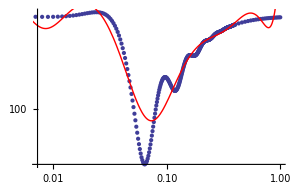

```mathematica
ϕ1r=ListLogLogPlot[{kvals,b1br+200}ᵀ,PlotStyle->Thick];
ω1r=LogLogPlot[b1brnw,{x,0.001,1},PlotStyle->Red];
Show[ϕ1r,ω1r]
```

### b2b2 fit

```mathematica
b2b2func=Interpolation[{kvals,b2b2}ᵀ];
b2b2nw=Fit[{kvals[[1;;420;;5]],b2b2[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^6},x];
```

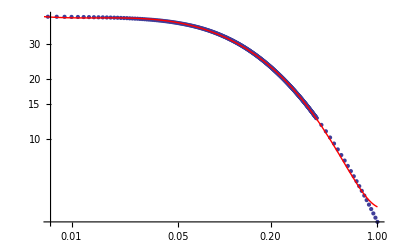

```mathematica
ϕ22=ListLogLogPlot[{kvals,b2b2}ᵀ,PlotStyle->Thick];
ω22=LogLogPlot[b2b2nw,{x,0.001,1},PlotStyle->Red];
Show[ ϕ22,ω22]
```

### b2br fit

```mathematica
b2brfunc=Interpolation[{kvals,b2br}ᵀ];
b2brnw=Fit[{kvals[[1;;420;;5]],b2br[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8,Log[x]^9, Log[x]^10},x]
```

2.38421+28.7886 Log[x]+107.627 Log[x]^2+184.375 Log[x]^3+170.117 Log[x]^4+90.7766 Log[x]^5+28.5827 Log[x]^6+5.15241 Log[x]^7+0.479004 Log[x]^8+0.0159179 Log[x]^9-0.000224146 Log[x]^10

```mathematica
b2brnwfunc[x_]:=2.3842063385136676+28.78855330193134 Log[x]+107.62725391236759 Log[x]^2+184.37515119018798 Log[x]^3+170.11724351441183 Log[x]^4+90.77664736732065 Log[x]^5+28.5826614515357 Log[x]^6+5.15241014890917 Log[x]^7+0.4790042071062025 Log[x]^8+0.01591787535830749 Log[x]^9-0.0002241459442930612 Log[x]^10
```

```mathematica
splice1=b2brnwfunc[#]&/@kvals[[1;;100]];
```

```mathematica
tail=Fit[{Log[kvals[[100;;350;;5]]],Log[b2br[[100;;350;;5]]]}ᵀ,{1,x},x]
```

-7.27382-3.71325 x

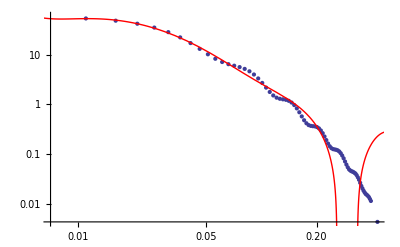

```mathematica
ϕ2r=ListLogLogPlot[{kvals[[1;;420;;5]],b2br[[1;;420;;5]]}ᵀ,PlotStyle->Thick];
ω2r=LogLogPlot[b2brnw,{x,0.001,1},PlotStyle->Red];
η2r=Plot[tail,{x,0.001,1},PlotStyle->{Green,Thick}]; (* Fix plot v loglogplot *)
Show[ ϕ2r,ω2r,η2r]
```

```mathematica
b2br
```

{58.0134,57.8679,57.6697,57.3534,56.9265,56.4794,55.9071,55.2809,54.5285,53.7908,52.9029,52.0058,51.0294,49.9787,48.8946,47.7308,46.5621,45.3427,44.0914,42.8035,41.4851,40.1592,38.82,37.4851,36.1081,34.7377,33.391,32.064,30.7245,29.4107,28.1241,26.8452,25.6161,24.3947,23.2189,22.0809,20.975,19.9111,18.9002,17.9215,16.9782,16.092,15.2511,14.4524,13.7027,12.9997,12.3357,11.7216,11.1448,10.6136,10.124,9.67475,9.26233,8.88745,8.54166,8.23234,7.95007,7.6968,7.46651,7.26458,7.08227,6.92253,6.76795,6.63794,6.52152,6.41234,6.31017,6.22164,6.13775,6.05678,5.97912,5.9036,5.82974,5.75418,5.68063,5.60255,5.51912,5.43495,5.34719,5.25608,5.15788,5.05681,4.95225,4.84277,4.72851,4.61249,4.49049,4.3666,4.24016,4.11163,3.98157,3.84871,3.7172,3.58551,3.45347,3.32092,3.19264,3.06594,2.94123,2.81948,2.69939,2.58474,2.47559,2.36899,2.26973,2.17365,2.08292,1.99763,1.91925,1.84445,1.77726,1.71477,1.65746,1.60304,1.55762,1.51523,1.47919,1.44409,1.41503,1.38871,1.36648,1.34927,1.33332,1.32018,1.30448,1.29861,1.29044,1.28415,1.27893,1.27179,1.26673,1.26105,1.25545,1.24902,1.24241,1.23652,1.22803,1.2173,1.20597,1.19485,1.1814,1.16694,1.14933,1.13053,1.11227,1.09203,1.06918,1.04712,1.0216,0.997145,0.970817,0.944789,0.916856,0.889253,0.860978,0.833341,0.805695,0.777751,0.750036,0.724387,0.697014,0.670327,0.645963,0.623184,0.597166,0.57551,0.554379,0.534715,0.515765,0.498552,0.482192,0.467796,0.453443,0.441271,0.430122,0.419852,0.411347,0.402942,0.395925,0.390621,0.385472,0.381273,0.377625,0.375063,0.373396,0.371695,0.369494,0.368182,0.367487,0.367952,0.366552,0.365923,0.365997,0.364541,0.363604,0.363168,0.361078,0.359238,0.357512,0.353991,0.35228,0.348893,0.344792,0.340224,0.336117,0.331718,0.326441,0.321055,0.314223,0.30873,0.301268,0.294763,0.288172,0.280317,0.272707,0.265457,0.258012,0.249571,0.242752,0.235066,0.22773,0.21972,0.213182,0.205766,0.199354,0.193075,0.186939,0.180423,0.175223,0.170006,0.16466,0.160453,0.155994,0.151774,0.148522,0.145228,0.142478,0.139733,0.137126,0.135164,0.13305,0.131795,0.130492,0.129041,0.12852,0.127231,0.126473,0.126734,0.126107,0.125341,0.125208,0.124726,0.124392,0.124201,0.124294,0.123353,0.123198,0.122244,0.121497,0.12088,0.120007,0.119245,0.118349,0.11687,0.115628,0.114079,0.112947,0.111334,0.109237,0.107498,0.105299,0.103326,0.101346,0.0991602,0.0970032,0.0946305,0.0923925,0.0899843,0.0876731,0.0853511,0.0831904,0.0806691,0.078061,0.0760511,0.0738359,0.0718449,0.0695527,0.0676982,0.0658697,0.0638459,0.0623069,0.060586,0.059022,0.057415,0.056272,0.0548727,0.0537044,0.0527382,0.0515817,0.0508304,0.04979,0.0493346,0.0487116,0.0481826,0.0476902,0.0472126,0.0469881,0.0465313,0.046193,0.0457572,0.0456092,0.0454491,0.0451051,0.0449178,0.0445521,0.0446313,0.0437557,0.0440355,0.0434178,0.0431878,0.0429565,0.0424336,0.0419498,0.0417594,0.0417234,0.0412246,0.0404227,0.039966,0.0393985,0.0389516,0.0382833,0.0376866,0.0368828,0.0361496,0.0355398,0.0345927,0.0340127,0.0334667,0.0322365,0.031838,0.0308599,0.0299679,0.0291081,0.0285616,0.0276071,0.0268283,0.0262493,0.0253851,0.0247342,0.0240261,0.0232619,0.022567,0.022137,0.0218005,0.0211669,0.020719,0.0201999,0.0197477,0.0194217,0.0187432,0.0186687,0.0182154,0.0179201,0.0174882,0.0172119,0.0172061,0.0169277,0.0166251,0.0164671,0.0160433,0.0160265,0.0159368,0.0157462,0.0154683,0.015271,0.0154288,0.0153348,0.0152616,0.0148806,0.0148534,0.0147081,0.0144766,0.0143894,0.0141018,0.0139944,0.0139352,0.0136273,0.0135558,0.013238,0.013091,0.0127845,0.0126655,0.0122472,0.0121151,0.0117838,0.0116227,0.011413,0.0109978,0.010646,0.0105183,0.00442262,0.00188255,-0.000605664,-0.00163042,-0.0025679,-0.00297799,-0.00322291,-0.00333149,-0.00333577,-0.00329774,-0.00319133,-0.00307501,-0.00292239,-0.00281332,-0.00263191,-0.00251093,-0.00236779,-0.00223167,-0.00212972,-0.0020227}

### brbr fit

```mathematica
brbrfunc=Interpolation[{kvals,brbr}ᵀ];
brbrnw=Fit[{kvals[[1;;420;;5]],brbr[[1;;420;;5]]}ᵀ,{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4,Log[x]^5,Log[x]^5,Log[x]^6,Log[x]^7,Log[x]^8},x];
```

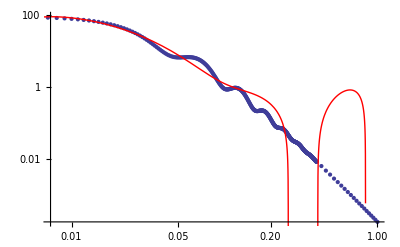

```mathematica
ϕrr=ListLogLogPlot[{kvals,brbr}ᵀ,PlotStyle->Thick];
ωrr=LogLogPlot[brbrnw,{x,0.001,1},PlotStyle->Red];
Show[ ϕrr,ωrr]
```

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

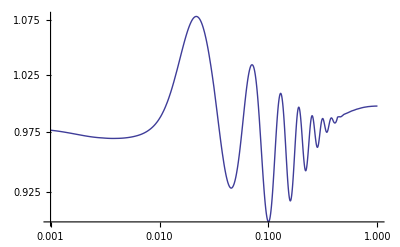

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

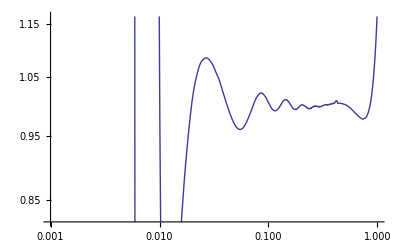

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

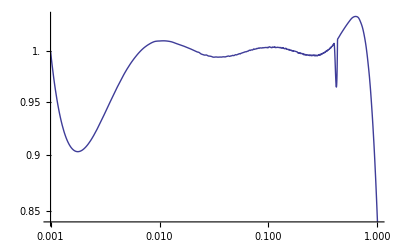

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

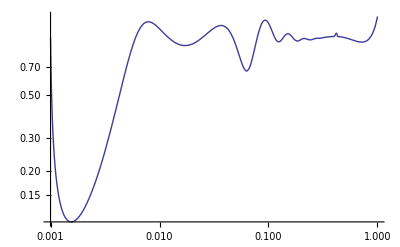

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

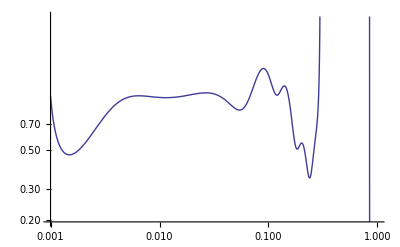

InterpolatingFunction::dmval: Input value {-6.90761416341001`} lies outside the range of data in the interpolating function. Extrapolation will be used.

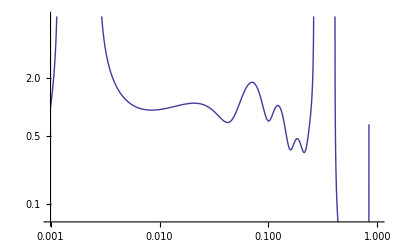

```mathematica
LogLogPlot[plinfunc[x]/psnwfunc[x],{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b1b2func[x]/b1b2nw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b2b2func[x]/b2b2nw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b1brfunc[x]/b1brnw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[b2brfunc[x]/b2brnw,{x,0.001,1},PlotStyle->Thick]
LogLogPlot[brbrfunc[x]/brbrnw,{x,0.001,1},PlotStyle->Thick]
```